# OptionsPattern Paradigm

## Tyson Jones tyson.jones@monash.edu August 2017

## For filtering and validating options

## basic structure

```mathematica
With[{a = 2 A}, #] & @ a
```

2 A

a = 2A would instead become some options = validating[raw options]. This entire structure can be put inside another function

```mathematica
(* don't actually need this;   declare accepted funcs in OptionsPattern, then just do OptionValue[{}]; 
checkOptions[
	options:OptionsPattern[],
	functions:_/;VectorQ[functions, MatchQ[_Symbol]]
] :=
	OptionValue[functions, {options}, {}];

checkOptions[
	options:OptionsPattern[],
	function:_Symbol
] :=
	checkOptions[options, {function}]
*)

extractOptions[
	options:OptionsPattern[],
	functions:_/;VectorQ[functions, MatchQ[_Symbol]]
] := 
	(* silently return only options for functions *)
	Sequence @@ FilterRules[{options}, Options /@ functions]
	
extractOptions[
	options:OptionsPattern[],
	function:_Symbol
] :=
	extractOptions[options, {function}]

addDefaultOptions[
	options:OptionsPattern[],
	functions:_/;VectorQ[functions, MatchQ[_Symbol]]
] :=
	Sequence @@ Flatten @ Join[{options}, Options /@ functions]
	
addDefaultOptions[
	options:OptionsPattern[],
	function:_Symbol
] :=
	addDefaultOptions[options, {function}]
	

(* not actually needed; just call purifyOptions and do the manual option checking; OptionValue[{}] 
validateOptions[
	options:OptionsPattern[],
	functions:_/;VectorQ[functions, MatchQ[_Symbol]]
] := (
	(* throw single error for bad options *)
	checkOptions[options, functions];
	
	(* return valid options *)
	extractOptions[options, functions]
)

validateOptions[
	options:OptionsPattern[],
	function:_Symbol
] :=
	validateOptions[options, {function}]
*)


(* only very dubiously works using Hold and Release
withValidOptions[
	rawOptions:OptionsPattern[],
	functions:_/;VectorQ[functions, MatchQ[_Symbol]]
] :=
	With[
		{options = validateOptions[rawOptions, functions]},
		#
	] &
*)
```

```mathematica
f [ validateOptions[
	poopy -> 3,
	wtf -> 5,
	PlotRange -> 10,
	AxesLabel -> 19,
	Paneled -> True,
	{Plot, Manipulate}
]]
```

OptionValue::nodef: Unknown option poopy for {Plot,Manipulate}.

OptionValue::nodef: Unknown option wtf for {Plot,Manipulate}.

f[PlotRange→10,AxesLabel→19,Paneled→True]

```mathematica
withValidOptions[
	poopy -> 3,
	wtf -> 5,
	PlotRange -> 10,
	AxesLabel -> 19,
	Paneled -> True,
	{Plot, Manipulate}
] @ f[options]
```

withValidOptions[poopy→3,wtf→5,PlotRange→10,AxesLabel→19,Paneled→True,{Plot,Manipulate}][f[options]]

```mathematica
testfunc[
	rawOptions:OptionsPattern[]
] :=
	Plot[x^2, {x, -1, 1}, options] //
	withValidOptions[rawOptions, {Plot}]
```

Plot::nonopt: Options expected (instead of options) beyond position 2 in Plot[x^2,{x,-1,1},options]. An option must be a rule or a list of rules.

OptionValue::nodef: Unknown option pop for {Plot}.

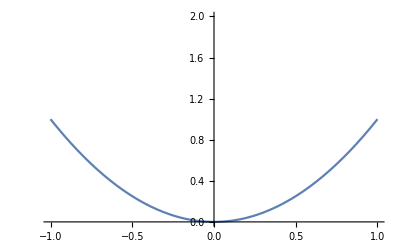

```mathematica
testfunc[PlotRange -> {0, 2}, pop -> 5]
```

It seems Plot with options gets evaluated (causing error), then options is valued, then Plot is re-evaluted.
While we can avoid this with something like...

```mathematica
testfunc2[
	rawOptions:OptionsPattern[]
] :=
	ReleaseHold[
		Hold[Plot[x^2, {x, -1, 1}, options]] //
		withValidOptions[rawOptions, {Plot}]
	]
```

```mathematica
testfunc2[PlotRange -> {0, 2}, poopoo -> 3]
```

OptionValue::nodef: Unknown option poopoo for {Plot}.

-Graphics-

this is even worse.
Decision;
we’ll just use a With! This is only used in the OUTER (public) functions anyway, so let’s not be pedantic about compactness

```mathematica
extractOptions =
```

```mathematica
testfunc3[
	rawOptions:OptionsPattern[]
] :=
	With[
		{options = validateOptions[rawOptions, {Plot, Manipulate}]},
		Manipulate[
			Plot[
				x + c, 
				{x, -5, 5}, 
				(* Evaluate @ FilterRules[{Echo[options]}, Options[Plot]] *)
				Evaluate @ extractOptions[options, Plot]
			],
			{c, 0, 1, .1},
			Evaluate @ extractOptions[options, Manipulate]
		]
	]
```

```mathematica
(* nah fuck it I still hate this *)
```

```mathematica
testfunc3[PlotRange -> 5, Paneled -> False, goose -> 9]
```

OptionValue::nodef: Unknown option goose for {Plot,Manipulate}.

```mathematica
(* let's do it like this *)
```

```mathematica
Options[testfunc4] := {
	xL -> -5,
	xR -> 5
};

testfunc4[
	options:OptionsPattern[{testfunc4, Plot, Manipulate}]
] := (
	(* alert on bad options *)
	OptionValue[{}];
	
	Manipulate[
		Plot[
			x + c, 
			{x, Quiet @ OptionValue[xL], Quiet @ OptionValue[xR]}, 
			Evaluate @ extractOptions[options, Plot]
		],
		{c, 0, 1, .1},
		Evaluate @ extractOptions[options, Manipulate]
	]
)
```

```mathematica
(******* ORRRR A BETTER IDEA; extract all locally used OptionValues ONCE with
```

```mathematica
testfunc4[PlotRange -> 5, Paneled -> False, xL -> -1, xR -> 1, poopoo -> 10]
```

OptionValue::nodef: Unknown option poopoo for {testfunc4,Plot,Manipulate}.

```mathematica
(* you could do something like; PlotWavefunction points to something private and filters the rules; ensures OptionValue is never accessed (eh nah fuck it that's awful too) *)
```